# Electrostatic analogy

```mathematica
$Assumptions={a>0,b>0,b>a,s>0,σ>0,x∈Reals,y∈Reals,y≠0,ν>0};
```

## Weak disorder ρ ~ 1/x

```mathematica
s=10;
σ=5;
a=Exp[(s-σ)/2];b=Exp[(s+σ)/2];
Φ[x_,y_]=0.5*Integrate[ Log[(x-X)^2+y^2]/(σ*X),{X,a,b}];
Ex[x_,y_]=Re[D[Φ[x,y],x]];
Ey[x_,y_]=Re[D[Φ[x,y],y]];
```

```mathematica
BoxSize=10;
x1=-10 ;
x2=100;
y1=-55;y2=55;
```

-10

100

```mathematica
Series[Log[(x-X)^2+y^2]/(σ*X),{x,0,1},{y,0,2}]
```

(Log[X^2]/(X σ)+y^2/(X^3 σ)+O[y]^3)+(-2/(X^2 σ)+(2 y^2)/(X^4 σ)+O[y]^3) x+O[x]^2

```mathematica
Normal[(Log[X^2]/(X σ)+y^2/(X^3 σ)+O[y]^3)+(-2/(X^2 σ)+(2 y^2)/(X^4 σ)+O[y]^3) x+O[x]^2]
```

x (-2/(X^2 σ)+(2 y^2)/(X^4 σ))+y^2/(X^3 σ)+Log[X^2]/(X σ)

```mathematica
Simplify[x (-2/(X^2 σ)+(2 y^2)/(X^4 σ))+y^2/(X^3 σ)+Log[X^2]/(X σ)]
```

(-2 x X^2+2 x y^2+X y^2+X^3 Log[X^2])/(X^4 σ)

```mathematica
Limit[Log[x]^2/x,x->0]
```

∞

```mathematica
a=Exp[(s-σ)/2];b=Exp[(s+σ)/2];
Integrate[(x (-2/(X^2 σ)+(2 y^2)/(X^4 σ))+y^2/(X^3 σ)+Log[X^2]/(X σ))/2,{X,a,b}]
```

```mathematica
Solve[s/2-(ⅇ^(-s/2-σ/2) (-1+ⅇ^σ) x)/σ+(ⅇ^(-3/2 (s+σ)) (-1+ⅇ^(3 σ)) x y^2)/(3 σ)+(ⅇ^-s y^2 Sinh[σ])/(2 σ)==s/2,x]
```

{{x→-(3 ⅇ^(s/2+(3 σ)/2) y^2 Sinh[σ])/(2 (-1+ⅇ^σ) (-3 ⅇ^(s+σ)+y^2+ⅇ^σ y^2+ⅇ^(2 σ) y^2))}}

```mathematica
Series[-(3 ⅇ^(s/2+(3 σ)/2) y^2 Sinh[σ])/(2 (-1+ⅇ^σ) (-3 ⅇ^(s+σ)+y^2+ⅇ^σ y^2+ⅇ^(2 σ) y^2)),{y,0,2}]
```

(ⅇ^(-s/2+σ/2) Sinh[σ] y^2)/(2 (-1+ⅇ^σ))+O[y]^3

```mathematica
Normal[(ⅇ^(-s/2+σ/2) Sinh[σ] y^2)/(2 (-1+ⅇ^σ))+O[y]^3]
```

(ⅇ^(-s/2+σ/2) y^2 Sinh[σ])/(2 (-1+ⅇ^σ))

```mathematica
Simplify[(ⅇ^(-s/2+σ/2) y^2 Sinh[σ])/(2 (-1+ⅇ^σ))]
```

```mathematica
ExpToTrig[1/4 ⅇ^(-s/2-σ/2) (1+ⅇ^σ) y^2]
```

1/4 y^2 (Cosh[s/2+σ/2]-Sinh[s/2+σ/2]) (1+Cosh[σ]+Sinh[σ])

```mathematica
FullSimplify[1/4 y^2 (Cosh[s/2+σ/2]-Sinh[s/2+σ/2]) (1+Cosh[σ]+Sinh[σ])]
```

1/2 ⅇ^(-s/2) y^2 Cosh[σ/2]

```mathematica
Expand[1/4 ⅇ^(-s/2-σ/2) (1+ⅇ^σ) y^2]
```

1/4 ⅇ^(-s/2-σ/2) y^2+1/4 ⅇ^(-s/2+σ/2) y^2

```mathematica
Series[Log[(x-X)^2+y^2]/(σ*X),{x,0,2},{y,0,2}]
```

(Log[X^2]/(X σ)+y^2/(X^3 σ)+O[y]^3)+(-2/(X^2 σ)+(2 y^2)/(X^4 σ)+O[y]^3) x+(-1/(X^3 σ)+(3 y^2)/(X^5 σ)+O[y]^3) x^2+O[x]^3

```mathematica
Normal[(Log[X^2]/(X σ)+y^2/(X^3 σ)+O[y]^3)+(-2/(X^2 σ)+(2 y^2)/(X^4 σ)+O[y]^3) x+(-1/(X^3 σ)+(3 y^2)/(X^5 σ)+O[y]^3) x^2+O[x]^3]
```

```mathematica
Integrate[x^2 (-1/(X^3 σ)+(3 y^2)/(X^5 σ))+x (-2/(X^2 σ)+(2 y^2)/(X^4 σ))+y^2/(X^3 σ)+Log[X^2]/(X σ),{X,a,b}]
```

s-(2 ⅇ^(-s/2-σ/2) (-1+ⅇ^σ) x)/σ+(2 ⅇ^(-3/2 (s+σ)) (-1+ⅇ^(3 σ)) x y^2)/(3 σ)+(3 ⅇ^(-2 (s+σ)) (-1+ⅇ^(4 σ)) x^2 y^2)/(4 σ)-(ⅇ^-s x^2 Sinh[σ])/σ+(ⅇ^-s y^2 Sinh[σ])/σ

```mathematica
pts1=Table[{Exp[x],0.001},{x,Log[a],Log[b],0.01}];
pts2=Table[{Exp[x],-0.001},{x,Log[a],Log[b],0.01}];
(*pts1=Table[{1/Sqrt[x],0.001},{x,a,b,0.01}];
pts2=Table[{1/Sqrt[x],-0.001},{x,a,b,0.01}];*)
```

```mathematica
g1=StreamPlot[{Ex[x,y],Ey[x,y]},{x,x1,x2},{y,y1,y2},StreamScale->Full,StreamPoints->{pts1,Automatic,100},StreamStyle->"Line"];
g2=StreamPlot[{Ex[x,y],Ey[x,y]},{x,x1,x2},{y,y1,y2},StreamScale->Full,StreamPoints->{pts2,Automatic,100},StreamStyle->"Line"];
```

```mathematica
g0=ContourPlot[Φ[x,y],{x,x1,x2},{y,y1,y2},ContourShading->None,Contours->20];
g=ContourPlot[Φ[x,y]==Log[2*Cosh[s/2]-2],{x,x1,x2},{y,y1,y2},ContourShading->None,ContourStyle->{Thick,Red}];
```

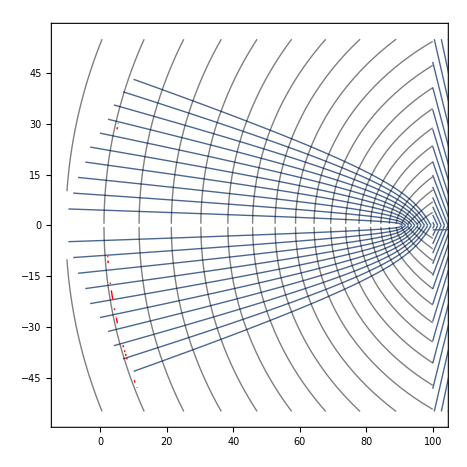

```mathematica
Show[g1,g2,g0,g,GridLines->{{0,a,b},{0}},GridLinesStyle->Thick]
```

# Strong disorder, ρ~x^2

```mathematica
Φ[x_,y_]=0.5*Integrate[3/(b^3-a^3)*Log[(x-X)^2+y^2]*X^2,{X,a,b}];
Ex[x_,y_]=Re[D[Φ[x,y],x]];
Ey[x_,y_]=Re[D[Φ[x,y],y]];
```

```mathematica
s=1;
σ=4;
a=Exp[s/2-σ/2];b=Exp[s/2+σ/2];
BoxSize=10;
x1=-BoxSize;
x2=BoxSize;
y1=-BoxSize;y2=BoxSize;
```

```mathematica
pts1=Table[{1/Sqrt[x],0.001},{x,a,b,0.01}];
pts2=Table[{1/Sqrt[x],-0.001},{x,a,b,0.01}];
```

```mathematica
(*g1=StreamPlot[{Ex[x,y],Ey[x,y]},{x,x1,x2},{y,y1,y2},StreamScale->Full,StreamPoints->{pts1,Automatic,100},StreamStyle->"Line"];
g2=StreamPlot[{Ex[x,y],Ey[x,y]},{x,x1,x2},{y,y1,y2},StreamScale->Full,StreamPoints->{pts2,Automatic,10},StreamStyle->"Line"];
*)
g1=StreamPlot[{Ex[x,y],Ey[x,y]},{x,x1,x2},{y,y1,y2},StreamScale->Full,StreamStyle->"Line"];
g2=StreamPlot[{Ex[x,y],Ey[x,y]},{x,x1,x2},{y,y1,y2},StreamScale->Full,StreamStyle->"Line"];
```

```mathematica
g0=ContourPlot[Φ[x,y],{x,x1,x2},{y,y1,y2},ContourShading->None,Contours->20];
g=ContourPlot[Φ[x,y]==Log[2*Cosh[s/2]-2],{x,x1,x2},{y,y1,y2},ContourShading->None,ContourStyle->{Thick,Red}];
```

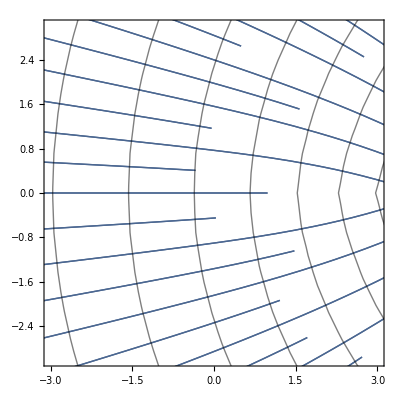

```mathematica
Show[g1,g2,g0,g,GridLines->{{0,a,b},{0}},GridLinesStyle->Thick,PlotRange->{{-3,3},{-3,3}}]
```

```mathematica
N[2*Cosh[s/2]-2]
```

0.255252

```mathematica
N[3/(b^3-a^3)]/4
```

0.000414816

```mathematica
N[a]
```

0.22313